```mathematica
Needs["ErrorBarPlots`"]
SetDirectory[DirectoryName[NotebookDirectory[],1]<>"\\Mathematica Packages"];
Get["Genealogy`"]
Get["SMARTree`"]
Get["Toolbox`"]
SetDirectory[NotebookDirectory[]]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

D:\Chaozhi\DirectoryUW\Project2_ARG\ARG_workfolder\SMARTree_MathematicaCode_May9\InferSMARTree

```mathematica
acf[x:{__Real},kk_Integer]:=Module[{p=Mean[x],l=Length[x]},Table[Sum[(x⟦t⟧-p) (x⟦t-k⟧-p),{t,k+1,l}]/(l-k)/Sum[((x⟦t⟧-p)^2)/l,{t,1,l}],{k,0,kk}]];f[n_,x_]:=1/2 (n-1) (1-Exp[-x/2])^(n-2) Exp[-x/2];
mf[n_]:=2 HarmonicNumber[n-1];
(*Clear[n,x]
Integrate[(x-mf[n])^2 f[n,x],{x,0,Infinity},Assumptions->(n>1)]*)
vf[n_]:=2/3 (π^2-6 PolyGamma[1,n])
cdff[n_,x_]:=(1-Exp[-x/2])^(n-1)
```

```mathematica
withdata=True;
bool=True;
primodel="P1"
ascertainmodel="M1"
id={"Standard","ExtraSeqs","ExtraBP","RecHotspot","RecMutHotspot"};
dataid=id[[1]];
datafile="Data_"<>dataid<>".txt";
outcold="SMARTree_OutCold_"<>ascertainmodel<>primodel<>"_"<>datafile
```

P1

M1

SMARTree_OutCold_M1P1_Data_Standard.txt

```mathematica
(*********************************************************************************************************)
```

```mathematica
getsnptbl[yls_,xls_]:=Module[{yls2,map},
yls2=If[yls[[-1,1]]==nbp,yls,Append[yls,{nbp,yls[[-1,2]]}]];
map=IndexByInterpolation[yls2[[All,1]]];
yls2[[map[xls],2]]
]
Block[{temp,seed},
temp=ReadList["TrueValues_"<>dataid<>".txt"];
If[Length[First[temp]]>6,
{nbp,nsq,truerho,truetheta,trueepsilon,seed,hotstart,hotwidth,hotratio}=First[temp],
{nbp,nsq,truerho,truetheta,trueepsilon,seed}=First[temp];
];
popunit=10^(-3);
truerho/=popunit;
truetheta/=popunit;
trueepsilon/=popunit;
If[Length[First[temp]]>6,
ls=Split[Rest[temp],Head[#1[[2]]]==Head[#2[[2]]]&];
errind=Flatten[ls[[1;;;;2]],1];
treels=Flatten[ls[[2;;;;2]],1];
treels=DeleteDuplicates[treels],
{errind,treels}=Split[Rest[temp],Head[#1[[2]]]==Head[#2[[2]]]&];
];
{truetreeloc,truetreels}=Transpose[treels];
truetreetbl=TotalBranchHeight[#]&/@truetreels;
ysnp=Rest[ReadList[datafile]];
trueaf=ysnp[[All,-1,1]];
prithetashape=1;
prithetascale=Infinity;
prithetamin=0;
prithetamax=0.01;
{prithetamin,prithetamax,prithetascale}/=popunit;
prirhoshape=1;
prirhoscale=Infinity;
prirhomin=0;
prirhomax=0.01;
{prirhomin,prirhomax,prirhoscale}/=popunit;
priepsmin=0;
priepsmax=0.1;
{priepsmin,priepsmax}/=popunit;
];

thetadist=If[prithetascale==Infinity,UniformDistribution[{prithetamin,prithetamax}],
TruncatedDistribution[{prithetamin,prithetamax},GammaDistribution[prithetashape,prithetascale]]]
rhodist=If[prirhoscale==Infinity,UniformDistribution[{prirhomin,prirhomax}],
TruncatedDistribution[{prirhomin,prirhomax},GammaDistribution[prirhoshape,prirhoscale]]]
epsdist=UniformDistribution[{prirhomin,priepsmax}]
```

UniformDistribution[{0,10.}]

UniformDistribution[{0,10.}]

UniformDistribution[{0,100.}]

```mathematica
Dimensions[#]&/@{ysnp,errind,treels}
```

{{130,3},{130,3},{65,2}}

```mathematica
Mean[Flatten[errind[[All,3]]]]//N
Tally[errind[[All,2]]]
```

0.00461538

{{1,127},{0,3}}

```mathematica
Dimensions[ysnp]
```

{130,3}

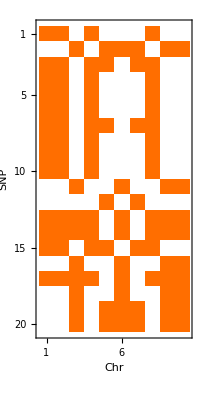

```mathematica
MatrixPlot[ysnp[[;;20,2]],MaxPlotPoints->Infinity,FrameLabel->{"SNP","Chr"}]
```

```mathematica
(*********************************************************************************************************)
```

```mathematica
tocoalescenttree[{tls_,al_}]:=Module[{tlist,alist,elist},
tlist=PadLeft[tls,2 Length[tls]-1];
alist=Most[al];
elist=SplitBy[SortBy[Transpose[{Range[Length[alist]],alist}],Last],Last];
CoalescentTree[tlist,elist]
];
```

```mathematica
rescold0=Drop[ReadList[outcold],0];//AbsoluteTiming
Dimensions[rescold0]
```

{0.4,Null}

{162,2,7}

```mathematica
burnin=-Floor[3 Length[rescold0]/6]
(*burnin=-2000;*)
thin=1;
If[1==1,
rescold=Join@@Table[rescold0[[burnin;;;;thin,i]],{i,Dimensions[rescold0][[2]]}],
rescold=rescold0[[burnin;;;;thin,1]];
];
rescold[[All,3,;;3]]/=popunit;
rescold[[All,4,All,2]]=Map[tocoalescenttree,rescold[[All,4,All,2]],{2}];//Timing
Dimensions[rescold]
```

-81

{0.156,Null}

{162,7}

```mathematica
(*****************************************************************************************************************)
```

{0.,Null}

{162,2,5}

-----------------------Start----------------------------

Geweke Convergence Diagnositics for the 2nd half chains:

Chain 1: 
 | logl | theta | epsilon | rho | #cp
Z-Score | -0.539962 | 1.89143 | 1.30107 | -0.127404 | 0.0390249
P-Value | 0.589223 | 0.0585664 | 0.193236 | 0.89862 | 0.968871

Chain 2: 
 | logl | theta | epsilon | rho | #cp
Z-Score | -0.191697 | 0.717363 | 0.342023 | -0.0600044 | -0.534701
P-Value | 0.84798 | 0.47315 | 0.732333 | 0.952152 | 0.592856

--------------------------------------------------------

Brooks, Gelman, and Rubin Convergence Diagnositics:

Potential Scale Reduction Factors for the 2nd half chains:
 | logl | theta | epsilon | rho | #cp
PSRF | 0.998302 | 1.02367 | 1.00965 | 0.994075 | 1.01346

Trace plot of PSRF:

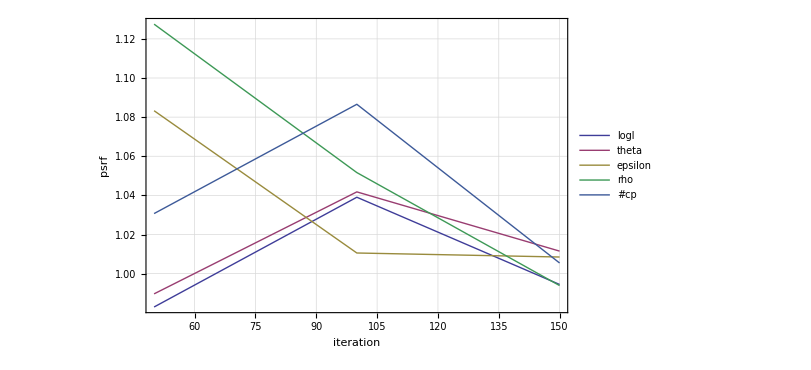

----------------------The End--------------------------

```mathematica
temp=Map[Join[{#[[2]]},Log[#[[3]]],{Log[N[Length[#[[4]]]]]}]&,rescold0,{2}];//Timing
Dimensions[temp]
MCMCDiagostic[temp[[2 burnin;;;;thin]],{"logl","theta","epsilon","rho","#cp"}]
```

```mathematica
thick=Thick
```

Thickness[Large]

```mathematica
linethick=0.003;
```

```mathematica
linegray=GrayLevel[0.65];
```

```mathematica
linestyle={Black,Thick}
```

{GrayLevel[0],Thickness[Large]}

```mathematica
(*****************************************************************************************************************)
```

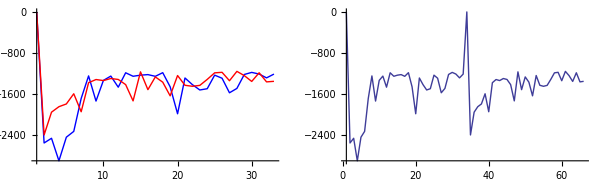

```mathematica
GraphicsRow[{ListLinePlot[Transpose[rescold0[[;;;;5,All,2]]],PlotStyle->{Blue,Red},PlotRange->All],ListLinePlot[Flatten[Transpose[rescold0[[;;;;5,All,2]]]],PlotRange->All]},ImageSize->600]
```

```mathematica
(*********************************************************************************************************)
```

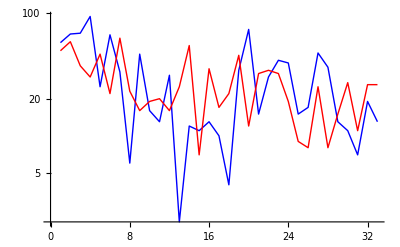
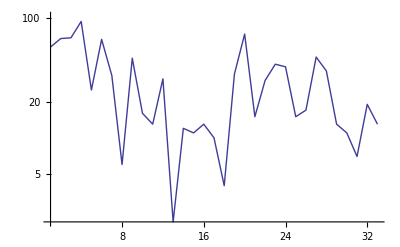
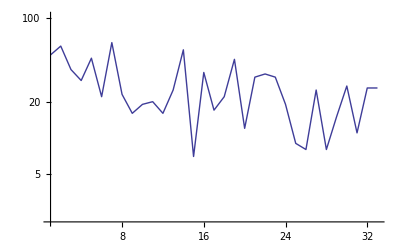

```mathematica
ls=Map[Length[#]&,rescold0[[;;;;5,All,4]],{2}];
Join[{ListLogPlot[Transpose[ls],PlotRange->All,Joined->True,PlotStyle->{Blue,Red}]},
Table[ListLogPlot[ls[[;;;;1,i]],Joined->True,PlotRange->{All,{Min[ls],1.1Max[ls]}}],{i,Dimensions[ls][[2]]}]
]
```

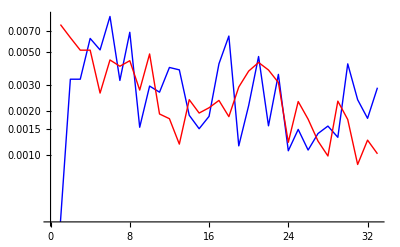
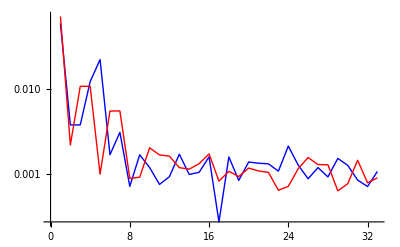
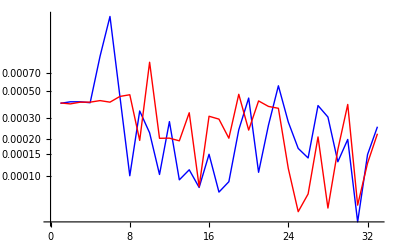

```mathematica
Table[ListLogPlot[Transpose[rescold0[[;;;;5,All,3,i]]],PlotRange->All,Joined->True,PlotStyle->{Blue,Red}],{i,3}]
```

```mathematica
(*********************************************************************************************************)
```

```mathematica
Clear[listmcplot,listhisplot]
listmcplot[mc_,truevalue_,lab_,withdata_,opts___]:=Module[{dim,g1,g2},
dim=Length[lab];
g1=Table[ListPlot[mc[[All,i]],Joined->True,PlotRange->All,AxesLabel->{"×"<>ToString[thin]<>" t",lab[[i]]}],{i,dim}];
g2=Table[ListPlot[{{0,truevalue[[i]]}},PlotMarkers->{Automatic,15},PlotRange->All,PlotStyle->{Blue,Red}],{i,dim}];
If[withdata,Show[#,opts]&/@Transpose[{g1,g2}],Show[#,opts]&/@g1]
];

listhisplot[mc_,truevalue_,lab_,withdata_,ticks_,opts___]:=Module[{dim,g1,g2,g11},
dim=Length[lab];
(*g1=Table[smoothHistogram[mc[[All,i]],20,{0,1},PlotRange->All,AxesOrigin->{Min[mc[[All,i]]],0},AxesLabel->{lab[[i]],"pdf"}],{i,dim}];*)
(*g11=Table[Histogram[mc[[All,i]],Automatic,"ProbabilityDensity",PlotRange->All,AxesLabel->{lab[[i]],"pdf"}],{i,dim}];*)
g1=Table[Histogram[mc[[All,i]],Automatic,"PDF",PlotRange->All,Ticks->ticks[[i]],AxesLabel->{lab[[i]],"pdf"}],{i,dim}];
g2=Table[ListPlot[{{truevalue[[i]],0}},PlotMarkers->{Automatic,25},PlotStyle->{Blue,Red}],{i,dim}];
If[withdata,Show[#,opts]&/@Transpose[{g1,g2}],Show[#,opts]&/@g1]
];
```

```mathematica
truehyper={truetheta,trueepsilon,truerho}
hyperlab={"θ","ε","r"};
reshyper=rescold[[All,3]];
Dimensions[reshyper]
Mean[reshyper]
```

{1.,1.,0.4}

{162,3}

{2.13089,1.07747,0.211562}

```mathematica
DistributionFitTest[reshyper[[All,1]],thetadist]
DistributionFitTest[reshyper[[All,2]],epsdist]
DistributionFitTest[reshyper[[All,3]],rhodist]
```

2.55351×10^-15

6.77236×10^-15

1.56541×10^-14

```mathematica
temp=MapThread[Join[{#1},#3,{#2}]&,{truehyper,Commonest[#]&/@Transpose[reshyper],Quantile[reshyper,{0.5,0.025,0.975}]}];
temp[[All,-1]]={Length[#],Mean[#]}&/@temp[[All,-1]];
Prepend[temp,{"true","q0.5","q0.025","q0.975","mode"}]//MatrixForm
```

(true | q0.5 | q0.025 | q0.975 | mode
1. | 1.84756 | 0.940202 | 4.67666 | {1,1.77575}
1. | 1.06039 | 0.450726 | 1.88444 | {1,0.706422}
0.4 | 0.177929 | 0.0425775 | 0.508656 | {2,0.25687})

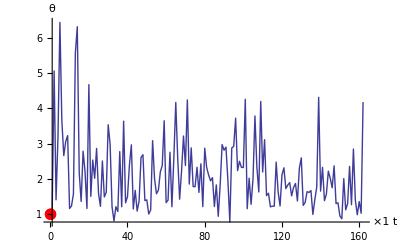
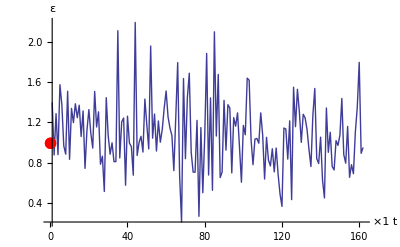
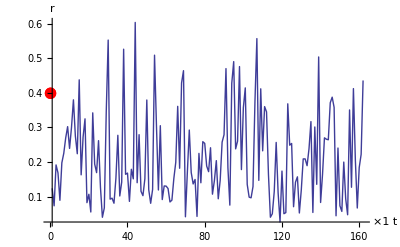

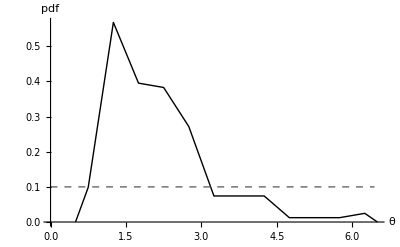
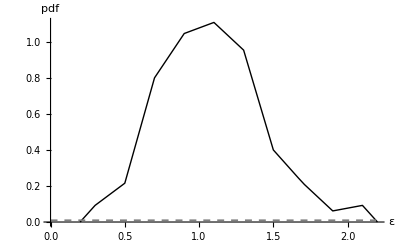
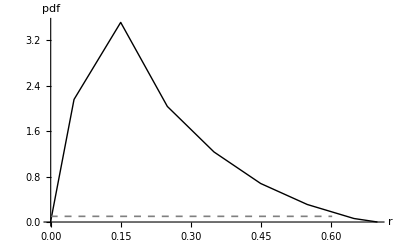

```mathematica
ticks={Automatic,{If[!withdata,Automatic,Automatic],Automatic},{Automatic,Automatic}};
gh1=listmcplot[reshyper,truehyper,hyperlab,withdata,LabelStyle->Directive[FontSize->14,FontFamily->"Times"]]
gh2=Table[PosteriorPDFPlot[reshyper[[All,i]],1,PlotRange->All,PlotRangePadding->None,PlotStyle->linestyle,AxesLabel->{hyperlab[[i]],"pdf"}],{i,Length[hyperlab]}];
pri1=Plot[PDF[thetadist,x],{x,0,Max[reshyper[[All,1]]]},PlotRange->All,PlotStyle->{Gray,Thickness[linethick],Dashed}];
pri2=Plot[PDF[epsdist,x],{x,0,Max[reshyper[[All,2]]]},PlotRange->All,PlotStyle->{Gray,Thickness[linethick],Dashed}];
pri3=Plot[PDF[rhodist,x],{x,0,Max[reshyper[[All,3]]]},PlotRange->All,PlotStyle->{Gray,Thickness[linethick],Dashed}];
gh3=Show[#,PlotRange->All,AxesOrigin->{0,0},PlotRangePadding->None]&/@Transpose[{gh2,{pri1,pri2,pri3}}]
```

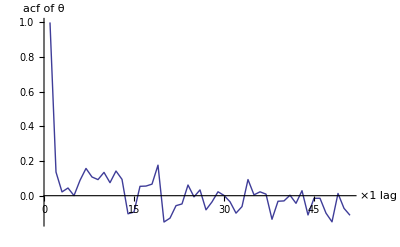
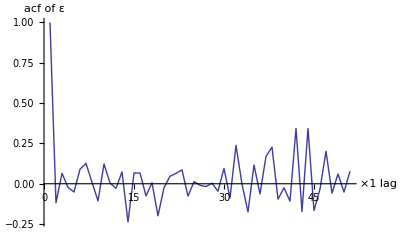
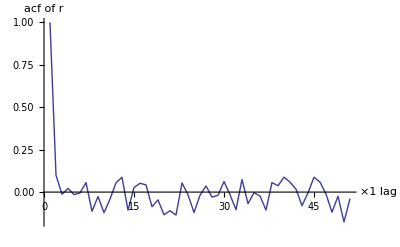

```mathematica
acfgh1=Table[ListLinePlot[acf[N[Take[reshyper[[All,i]]],Min[500,Length[reshyper]]],50],AxesOrigin->{0,0},AxesLabel->{"×"<>ToString[thin]<>" lag","acf of "<>hyperlab[[i]]},PlotRange->All],{i,Length[hyperlab]}]
```

```mathematica
(*********************************************************************************************************)
```

```mathematica
(*********************************************************************************************************)
```

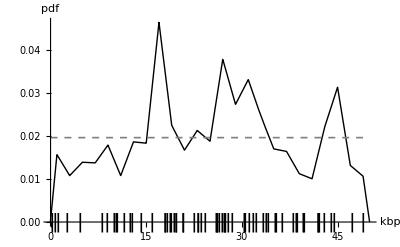

```mathematica
ls=DeleteCases[Flatten[rescold[[All,4,All,1]]],1]/1000;
gcp=Show[PosteriorPDFPlot[ls,1,PlotRange->All,PlotRangePadding->None,PlotStyle->linestyle,AxesLabel->{"x","pdf"}],Plot[PDF[UniformDistribution[{0,nbp/1000+1}],x],{x,0,nbp/1000},PlotStyle->{Gray,Thickness[linethick],Dashed}],AxesLabel->{"kbp","pdf"}];
If[withdata,gcp=Show[gcp,ListPlot[Thread[{Rest[truetreeloc/1000],0}],PlotMarkers->{"|",20},PlotStyle->Black]]];
gcp
```

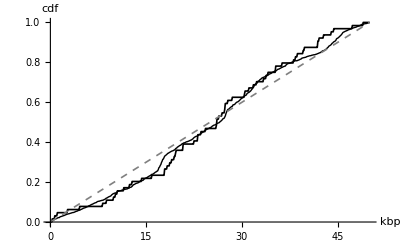

```mathematica
dist1=EmpiricalDistribution[Rest[truetreeloc/1000]];
dist2=EmpiricalDistribution[DeleteCases[Flatten[rescold[[All,4,All,1]]],1]/1000];
gcpcpf=Show[
DiscretePlot[{CDF[dist1,x],CDF[dist2,x]},{x,0,nbp/1000.,0.1},Filling->None,Joined->True,PlotStyle->{{Black,Thickness[linethick]},linestyle}],Plot[x/(nbp/1000),{x,0,nbp/1000},PlotStyle->{Gray,Thickness[linethick],Dashed}],AxesLabel->{"kbp","cdf"}]
```

```mathematica
If[nsq==10&&nbp==500000,
dist1=EmpiricalDistribution[Select[Rest[truetreeloc/1000],#≤50&]];
dist2=EmpiricalDistribution[Select[DeleteCases[Flatten[rescold[[All,4,All,1]]],1]/1000,#≤50&]];
gcpcdf50=Show[
DiscretePlot[{CDF[dist1,x],CDF[dist2,x]},{x,0,50,0.1},Filling->None,Joined->True,PlotStyle->{{Black,Thickness[linethick]},linestyle}],Plot[x/(50),{x,0,50},PlotStyle->{Gray,Thickness[linethick],Dashed}],AxesLabel->{"kbp","cdf"}]
]
```

```mathematica
(*********************************************************************************************************)
```

```mathematica
(*********************************************************************************************************)
```

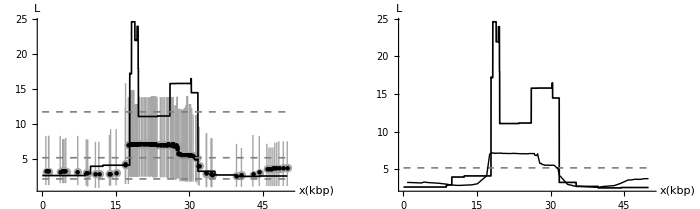

```mathematica
restbl=rescold[[All,4,All,{1,3}]];
pos=ysnp[[All,1]];
tblsnp=getsnptbl[#,pos]&/@restbl;
lev={0.025,0.5,0.975};
qtbl=Quantile[tblsnp,lev];
priq=(FindRoot[cdff[nsq,x]==#,{x,2}]&/@lev)[[All,1,2]];
If[withdata,
truetbl=getsnptbl[Transpose[{truetreeloc,truetreetbl}],pos],
truetbl=Table[mf[nsq],{Length[pos]}]
];

ls=Transpose[{truetbl,qtbl[[All,2]]}];
errls=Table[{{pos[[i]]/1000,qtbl[[i,2]]},ErrorBar[qtbl[[i,{1,3}]]-qtbl[[i,2]]]},{i,Length[qtbl]}];
g=ErrorListPlot[errls,PlotRange->All,AxesLabel->{"x(kbp)","L"},PlotStyle->linegray,PlotMarkers->{Automatic,0}];
g=Show[g,ListPlot[errls[[All,1]],PlotMarkers->{Automatic,6},PlotStyle->Black]];
If[withdata,
ls=Transpose[{(Append[truetreeloc,nbp+1]-1 )/1000.,Prepend[truetreetbl,First[truetreetbl]]}];
ls=DeleteDuplicates[ls];
truetblf=Interpolation[ls,InterpolationOrder->0];
g2=Plot[truetblf[x],{x,0,nbp/1000},PlotStyle->{Black,Thickness[linethick]},PlotRange->All]
];
g3=Plot[priq,{x,0,nbp/1000+0.5},PlotStyle->{{Gray,Thickness[linethick],Dashed}}];
gtbl=Show[If[withdata,{g,g2,g3},{g,g3}],AxesOrigin->{-1,0},PlotRangePadding->None];
gtbl2=Show[g2,
Plot[priq[[2]],{x,0,nbp/1000+0.5},PlotStyle->{{Gray,Thickness[linethick],Dashed}}],
ListLinePlot[Transpose[{pos/1000,qtbl[[All,2]]}],PlotStyle->linestyle],
PlotRange->{{0,All},{0,All}},AxesOrigin->0,AxesLabel->{"x(kbp)","L"}
];
If[nsq==10&&nbp==500000,
gtbl50=Show[
Plot[truetblf[x],{x,0,50},PlotStyle->{Black,Thickness[linethick]},PlotRange->All],
Plot[priq[[2]],{x,0,50},PlotStyle->{{Gray,Thickness[linethick],Dashed}}],
ListLinePlot[Select[Transpose[{pos/1000,qtbl[[All,2]]}],First[#]≤50&],PlotStyle->linestyle],
PlotRange->{{0,All},{0,All}},AxesOrigin->0,AxesLabel->{"x(kbp)","L"}
];
GraphicsRow[{gtbl,gtbl2,gtbl50},ImageSize->1000],
GraphicsRow[{gtbl,gtbl2},ImageSize->700]
]
```

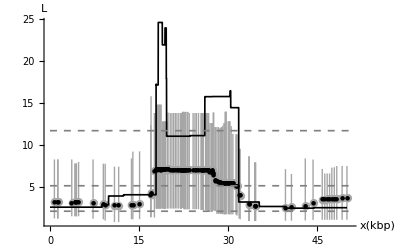
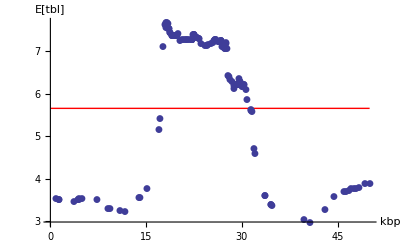
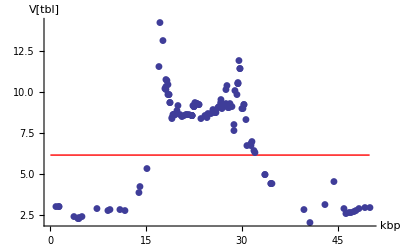

```mathematica
{gtbl,
Show[ListPlot[Transpose[{pos/1000,Mean[tblsnp]}],PlotMarkers->Automatic,AxesLabel->{"kbp","E[tbl]"}],Plot[mf[nsq],{x,0,nbp/1000},PlotStyle->{Thick,Red}],PlotRange->All],
Show[ListPlot[Transpose[{pos/1000,Variance[tblsnp]}],PlotMarkers->Automatic,AxesLabel->{"kbp","V[tbl]"}],Plot[vf[nsq],{x,0,nbp/1000},PlotStyle->{Thick,Red}],PlotRange->All]}
```

```mathematica
If[!withdata,
gtbl2=ListPlot[100 {(Mean[tblsnp]-mf[nsq])/mf[nsq],(Variance[tblsnp]-vf[nsq])/vf[nsq]},PlotStyle->{Brown,Blue},PlotMarkers->Automatic,Joined->True,AxesLabel->{"Site","100 (est-pri)/pri" },AxesOrigin->{0,0},PlotRange->{{0,Dimensions[tblsnp][[2]]+1},All}]
]
```

{0.0156,Null}

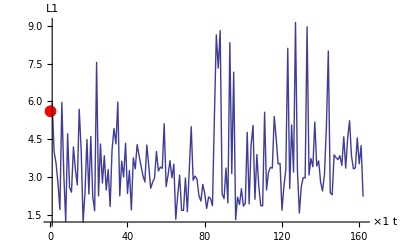
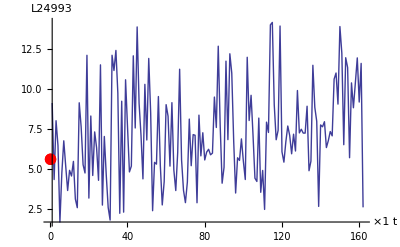
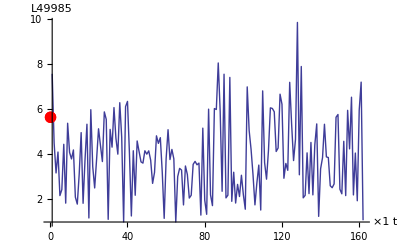

{0.1716,Null}

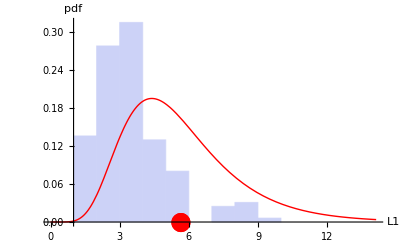
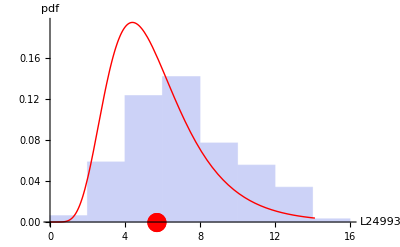
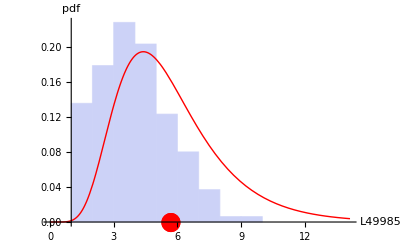

```mathematica
pos={1,ysnp[[-1,1]]};
pos=Insert[pos,Floor[Mean[pos]],2];
tbl2=getsnptbl[#,pos]&/@restbl;//Timing
truetbl=getsnptbl[Transpose[{truetreeloc,truetreetbl}],pos];
truetbl=Table[mf[nsq],{Length[pos]}];
tbllab="L"<>ToString[#]&/@pos;
pritbl=Plot[f[nsq,x],{x,0,Max[tbl2]},PlotRange->All,PlotStyle->{Red,Thick}];
g1tbl=listmcplot[tbl2,truetbl,tbllab,withdata,LabelStyle->Medium]
g2tbl=Table[ListLinePlot[acf[N[tbl2[[All,i]]],100],AxesOrigin->{0,0},AxesLabel->{"×"<>ToString[thin]<>" lag","acf of "<>tbllab[[i]]},PlotRange->All],{i,Length[tbllab]}];//Timing
g3tbl=listhisplot[tbl2,truetbl,tbllab,withdata,Table[Automatic,{3}],LabelStyle->Medium];
g3tbl=Show[{#,pritbl},PlotRange->All]&/@g3tbl
```

```mathematica
(*********************************************************************************************************)
```

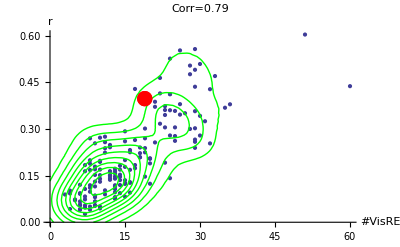

```mathematica
i=3;
ls=Table[Count[SameCoalescentTreeQ@@#&/@Partition[rescold[[k,4,All,2]],2,1],False],{k,Length[rescold]}];
ls=Transpose[{ls,reshyper[[All,i]]}];
gcorcp=Show[
ListPlot[ls,AxesOrigin->{0,0},PlotRange->All,PlotLabel->Style["Corr="<>ToString[Round[Correlation[ls[[All,1]],ls[[All,2]]],0.01]],20],AxesLabel->{"#VisRE",hyperlab[[i]]}],
ContourPlot[Evaluate@PDF[SmoothKernelDistribution[ls],{x,y}],{x,0,Max[ls[[All,1]]]},{y,0,Max[ls[[All,2]]]},ContourShading->None,PlotRange->All,ContourStyle->Directive[Green]]
];
If[withdata,gcorcp=Show[gcorcp,ListPlot[{{Count[SameCoalescentTreeQ@@#&/@Partition[truetreels,2,1],False],truehyper[[i]]}},PlotStyle->Red,PlotMarkers->{Automatic,20}]]
];
gcorcp
```

{θ,ε,r}

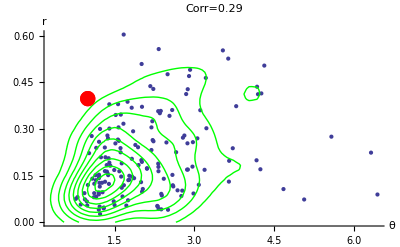
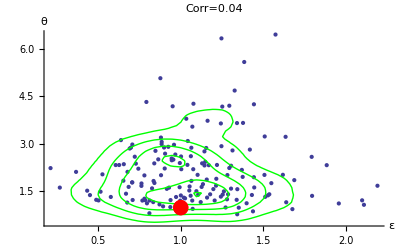
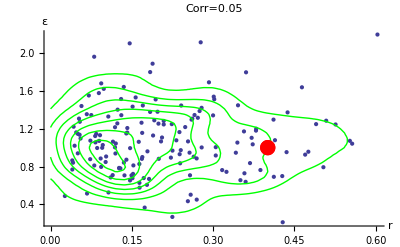

```mathematica
hyperlab
ijls={{1,3},{2,1},{3,2}};
gcorhyper=Table[
{i,j}=ij;
ls=reshyper[[All,{i,j}]];
gg=Show[
ListPlot[ls,AxesOrigin->{0,0},PlotRange->All,PlotLabel->Style["Corr="<>ToString[Round[Correlation[ls[[All,1]],ls[[All,2]]],0.01]],20],AxesLabel->{hyperlab[[i]],hyperlab[[j]]}],
ContourPlot[Evaluate@PDF[SmoothKernelDistribution[ls],{x,y}],{x,0,Max[ls[[All,1]]]},{y,0,Max[ls[[All,2]]]},ContourShading->None,PlotRange->All,ContourStyle->Directive[Green]]
];
If[withdata,gg=Show[gg,ListPlot[{truehyper[[{i,j}]]},PlotStyle->Red,PlotMarkers->{Automatic,20}]]
];
gg,{ij,ijls}]
```

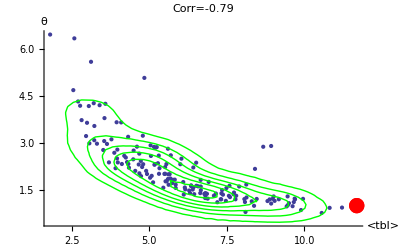
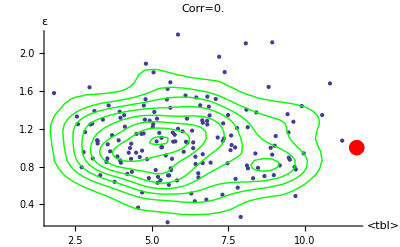
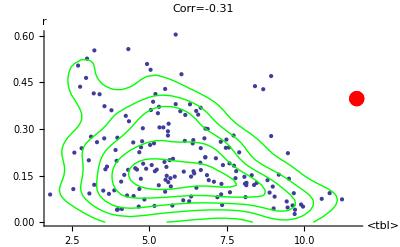

```mathematica
truemtbl=Mean[getsnptbl[Transpose[{truetreeloc,truetreetbl}],ysnp[[All,1]]]];
mtbl=Mean[Transpose[tblsnp]];
gcortbl=Table[
ls=Transpose[{mtbl,reshyper[[All,i]]}];
gg=Show[
ListPlot[ls,AxesOrigin->{0,0},PlotRange->All,PlotLabel->Style["Corr="<>ToString[Round[Correlation[ls[[All,1]],ls[[All,2]]],0.01]],20],AxesLabel->{"<tbl>",hyperlab[[i]]}],
ContourPlot[Evaluate@PDF[SmoothKernelDistribution[ls],{x,y}],{x,0,Max[ls[[All,1]]]},{y,0,Max[ls[[All,2]]]},ContourShading->None,PlotRange->All,ContourStyle->Directive[Green]]
];
If[withdata,gg=Show[gg,ListPlot[{{truemtbl,truehyper[[i]]}},PlotStyle->Red,PlotMarkers->{Automatic,20}]]];
gg,{i,3}]
```

```mathematica
(*********************************************************************************************************)
```

```mathematica
(*********************************************************************************************************)
```

true visible #RE=19

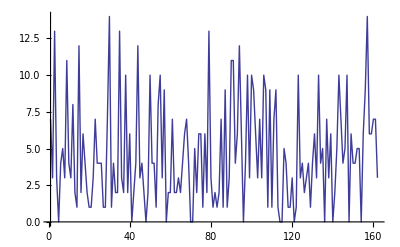
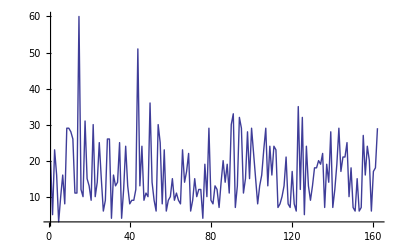
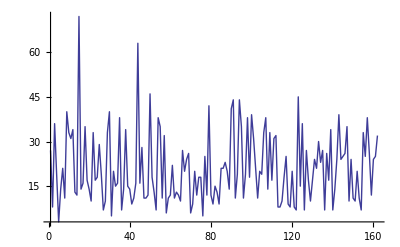

{{0,4,13},{5,14,33},{6,18,44},{0.,0.2,0.411765}}

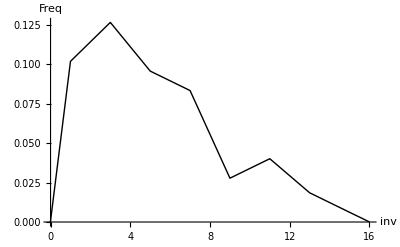
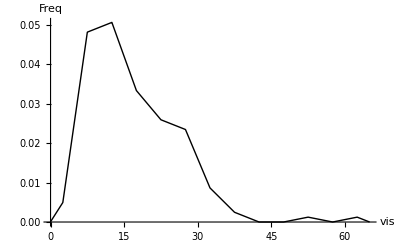
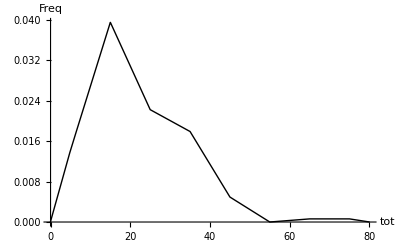
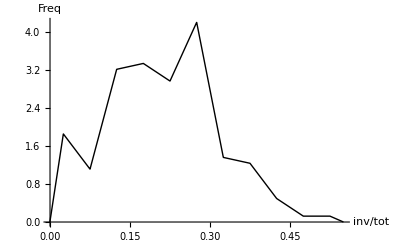

```mathematica
Print["true visible #RE=",Count[SameCoalescentTreeQ@@#&/@Partition[truetreels,2,1],False]]
ind=Table[Boole[SameCoalescentTreeQ@@#&/@Partition[rescold[[k,4,All,2]],2,1]],{k,Length[rescold]}];
ntot=Length[#]&/@ind;
ninv=Total[ind,{2}];
nvis=ntot-ninv;
{ListLinePlot[ninv,PlotRange->All],ListLinePlot[nvis,PlotRange->All],ListLinePlot[ntot,PlotRange->All]}
Quantile[Select[#,NumberQ],{0.025,0.5,0.975}]&/@{ninv,nvis,ntot,N[ninv/ntot]}
gnRE=MapThread[PosteriorPDFPlot[#1,1,PlotStyle->linestyle,PlotRange->All,AxesLabel->{#2,"Freq"}]&,{{ninv,nvis,ntot,ninv/ntot},{"inv","vis","tot","inv/tot"}}]
```

```mathematica
(*********************************************************************************************************)
```

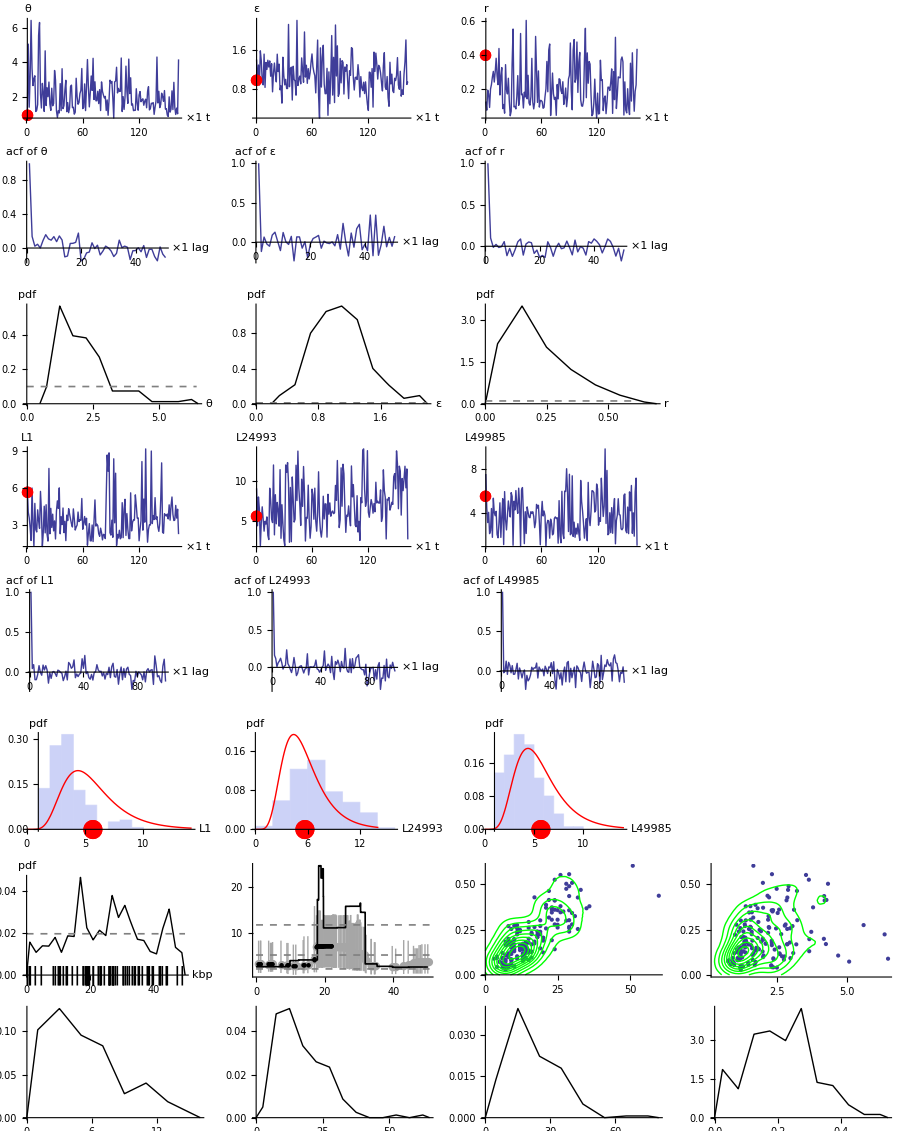

```mathematica
out=GraphicsGrid[{gh1,acfgh1,gh3,g1tbl,g2tbl,g3tbl,{gcp,gtbl,gcorcp,gcorhyper[[1]]},gnRE},ImageSize->900]
```

```mathematica
(*********************************************************************************************************)
```

```mathematica
mapfun=Function[{x},
Module[{sls,trls,yls},
{sls,trls}=Transpose[x];
yls=ysnp[[All,1]];
trls[[IndexByInterpolation[Append[sls,nbp+1]][yls]]]
]
];
```

```mathematica
nminor=Total[ysnp[[All,2]],{2}];
If[1==1,nminor=nminor/.{x_/;x≥nsq/2:>nsq-x}];
```

```mathematica
restr=rescold[[All,4,All,;;2]];
restr=Map[mapfun,restr];//Timing
truetrees=mapfun[Transpose[{truetreeloc,truetreels}]];//Timing
restr=N[Map[MapThread[TreeRFDistance,{truetrees,#}]&,restr]];//Timing
```

{0.2808,Null}

{0.0156,Null}

{4.18083,Null}

```mathematica
(*********************************************************************************************************)
```

```mathematica
(*********************************************************************************************************)
```

True

{12.2154,16.,16.}

i=1;True

i=3;True

i=5;True

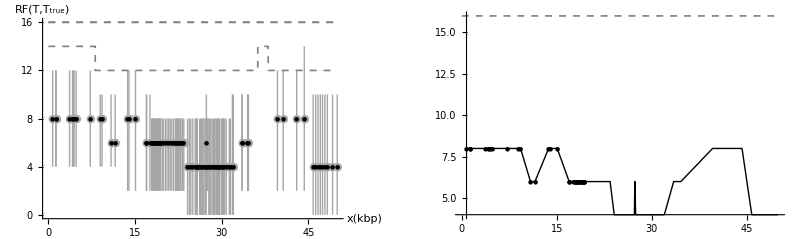

```mathematica
level={0.025,0.5,0.975};
ls=Quantile[restr,level];
errls=Transpose[{Transpose[{ysnp[[All,1]]/1000.,ls[[All,2]]}],ErrorBar[#]&/@Transpose[{ls[[All,1]]-ls[[All,2]],ls[[All,3]]-ls[[All,2]]}]}];
g=ErrorListPlot[errls,PlotRange->{All,{-0.05,1}},PlotMarkers->{Automatic,0},PlotStyle->linegray];
g=Show[g,ListPlot[errls[[All,1]],PlotMarkers->{Automatic,6},PlotStyle->Black]];
priqdist=ReadList["priTreeRFDistance_"<>dataid<>".txt"];
truetreeloc==priqdist[[All,1]]
N[Mean[priqdist[[All,-1,{1,3,5}]]]]
g30=Table[
ls=Transpose[{(Append[priqdist[[All,1]],nbp+1]-1 )/1000.,Prepend[priqdist[[All,-1,i]],First[priqdist[[All,-1,i]]]]}];
ls=DeleteDuplicates[ls];
priq=Interpolation[ls,InterpolationOrder->0];
Print["i=",i,";",priq[ls[[All,1]]]==ls[[All,2]]];
Plot[priq[x],{x,0,nbp/1000},PlotStyle->{Gray,Thickness[linethick],Dashed},PlotPoints->100,PlotRange->All],{i,{1,3,5}}];
Transpose[{priqdist[[All,1]]/1000.,priqdist[[All,-1,1]]}];
g3=Show[g30];
gtrcor=Show[{g,g3},AxesOrigin->{-1,-0.05},PlotRangePadding->None,PlotRange->All,PlotRange->All,AxesLabel->{"x(kbp)","RF(T,T_true)"}];
gtrcor2=Show[
ListPlot[errls[[All,1]],PlotRange->All,PlotMarkers->{Automatic,6},Joined->True,PlotStyle->linestyle],
g30[[3]],PlotRangePadding->None,AxesLabel->{"x(kbp)","RF(T,T_true)"}];
GraphicsGrid[{{gtrcor,gtrcor2}},ImageSize->800]
```

```mathematica
(*********************************************************************************************************)
```

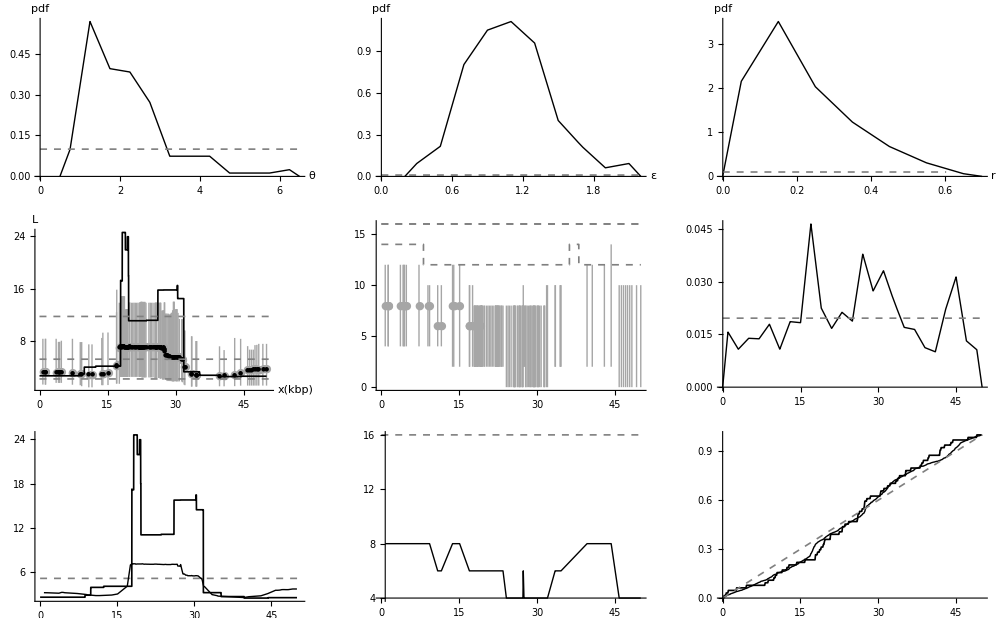

```mathematica
ggmx={gh3[[{1,2,3}]],{gtbl,gtrcor,gcp},{gtbl2,gtrcor2,gcpcpf}};
ggoutput=GraphicsGrid[ggmx,ImageSize->1000]
```

```mathematica
(*********************************************************************************************************)
```